```mathematica
(*This chapter is basically an application of the previous one, so we'll write our note in Mathematica instead of Typst*)
(*First, let's import the poverty and economic growth data from data.csv*)
data=Import["C:/Users/genshin/Documents/note/running-regressions/poverty-and-economic-growth/data.csv","CSV"];
First[data](*To show and confirm the header of the table, optional for data research in a notebook*)
data=Rest[data][[All,{1,2,3}]];(*Strip the header from the table, extract first three columns and drop the rest of them for each row*)
```

{country,poverty_rate_change_pct,gdp_growth_pct,exports_change_pct,investment_change_pct}

{{Lao PDR,-2.,3.5},{Bangladesh,-3.4,3.3},{Uganda,-16.1,3.1},{Bhutan,-19.2,3.},{Cape Verde,-6.3,2.9},{Mozambique,-3.6,2.5},{Nepal,-14.3,2.4},{Solomon Islands,-4.1,1.4},{Benin,-6.1,1.},{Malawi,-20.4,0.9},{Ethiopia,-1.2,0.8},{Lesotho,22.3,0.7},{Burkina Faso,-6.5,0.4},{Mali,8.7,0.1},{Senegal,0.8,0.},{Central African Republic,23.3,-0.8},{Chad,2.5,-1.3},{Vanuatu,3.5,-1.3},{Guinea-Bissau,25.,-1.6},{Madagascar,4.5,-1.8},{Comoros,11.8,-3.5},{Angola,1.5,-3.8},{Mauritania,-6.2,1.6},{Guinea,-7.4,0.8},{Gambia,-16.3,-0.9},{Togo,-1.7,-2.},{Niger,5.1,-2.},{Rwanda,13.1,-2.9},{Burundi,11.,-3.4},{Haiti,14.9,-3.5},{Sierra Leone,37.2,-5.7}}

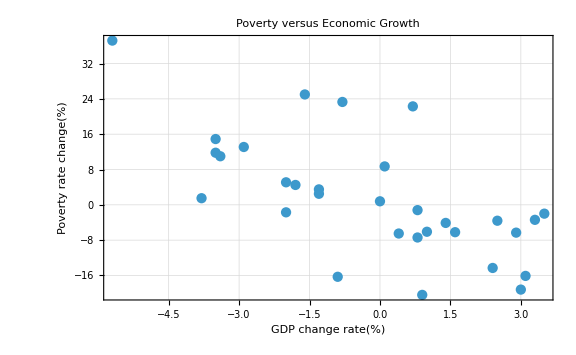

```mathematica
(*First, plot the data out for a quick glimpse on it, to check whether out hypothesis is firm or not*)
dataPlot=ListPlot[data[[All,{3,2}]],AxesLabel->{"GDP change rate(%)","Poverty rate change(%)"},PlotLabel->"Poverty versus Economic Growth",GridLines->Automatic,Frame->True,ImageSize->Large]
```

```mathematica
(*OK, the data seems to have some certain negative relationship between GDP change and poverty rate, so we can go on to have a deeper check*)
(*We're now checking the correlation between two data sets. Note that for single variable regression, there's no difference between "dependent" and "independent" variable, we can switch their order arbitrarily for pure correlation purpose*)
Correlation[data[[All,{3}]],data[[All,{2}]]](*According to the answer, r should be about -0.66*)
```

{{-0.666028}}

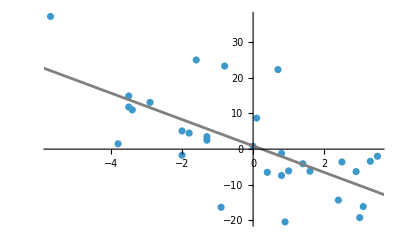

```mathematica
(*We've already seen the result strongly suggest that there are negative relationship between poverty and economic growth*)
(*Now let's do a real ordinary least square(OLS)*)
model=LinearModelFit[data[[All,{3,2}]],x,x];
Show[ListPlot[data[[All,{3,2}]]],Plot[model[x],{x,-6,4},PlotStyle->Gray]](*Show the figure with a fitted line*)
```

```mathematica
(*Thanks to the great power of Mathematica, we can check "how well does the model fit the data"(via R^2) by simply checking the "RSquared" segment from the return value of LinearModelFit*)
model["RSquared"](*The value is about 0.44, which indicates that the explanatory variable contributes to about 44% of the variance of the regressand*)
```

```mathematica
(*After checking the R^2 value, we're interested in how "confident" we can be to our hypothesis, this will lead to Student's t test*)
(*Again, thanks to the great power of Mathematica, what we need to do is merely print "ParameterTable" out*)
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.897221 | 1.85797 | 0.482903 | 0.63279
x | -3.70265 | 0.770048 | -4.80834 | 0.0000432059

```mathematica
(*As we can see, the t-Statistic of x and intercept param. are shown as listed. The p-value of x is far below 0.05, so we're quite sure that there must be some relationship between economic growth and poverty rate*)
(*To know the details of hypothesis test, see "appendix.typ"*)
```